## General Functions

```mathematica
CL=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
FWHMtoWaist[FWHM_]:=FWHM/(2Sqrt[1/2Log[2]])
```

```mathematica
Clear[GaussFitI];
GaussFitI[Data_,ShowPlot_:False]:=Module[{minFrequ,fit,output},
minFrequ=Data[[Position[Data[[All,2]],Min[Data[[All,2]]]][[1,1]],1]];
fit=NonlinearModelFit[Data,1-o-a Exp[-2(f-f0)^2/FWHMtoWaist[FWHM]^2],{{f0,minFrequ},{o,0.8},{a,0.8},{FWHM,1}},f];
output=If[ShowPlot,
{fit,
Show[
ListPlot[{Data,Data},PlotRange->All,Joined->{True,False},PlotStyle->{CL[[1]],CL[[1]]},ImageSize->600],
Plot[fit[x],{x,Min[Data[[All,1]]],Max[Data[[All,1]]]},PlotStyle->Red,PlotRange->All]]},
fit]
];
```

```mathematica
Clear[ZeroToOne];
ZeroToOne[data_]:=Module[{minVal,maxVal},
minVal=Min[data[[All,2]]];
maxVal=Max[data[[All,2]]];
data/.{x_,y_}:>{x,(y-minVal)/(maxVal-minVal)}
];
```

```mathematica
Clear[FunctionI];
FunctionI[Path_]:=Module[{FileName,ImportData, output},
FileName=StringSplit[Path,"\\"][[-1]]<>".txt";
ImportData= Import[Path<>"\\"<>FileName,"Table"][[2;;-1]];
output=ZeroToOne[ImportData[[All,{1,2}]]]
];
```

## Readin and analyze data

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::munfl: 1/2^1446.99 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2^7409.86 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2^20978.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

Divide::infy: Infinite expression (2.47219×10^-308)/0. encountered.

Divide::infy: Infinite expression -(6.8426×10^-292)/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

LinearAlgebra`BLAS`TRSV::mindet: Input matrix contains an indeterminate entry.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

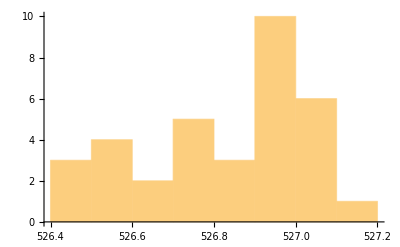
{-Graphics-,526.825,0.204456,34}

```mathematica
ReadinPath202303=NotebookDirectory[]<>"\\mass_spec_data\\TrapFrequRef\\2023_03";
FileNamesList202303=FileNames["*",ReadinPath202303,1];
DataTable202303=Table[FunctionI[FileNamesList202303[[k]]],{k,1,Length[FileNamesList202303]}];
FitTable202303=Table[GaussFitI[DataTable202303[[k]],True],{k,1,Length[DataTable202303]}];
{Histogram[FitTable202303[[All,1,1,2,1,2]],10],Mean[FitTable202303[[All,1,1,2,1,2]]],StandardDeviation[FitTable202303[[All,1,1,2,1,2]]],Length[FitTable202303[[All,1,1,2,1,2]]]}
```

## Plots

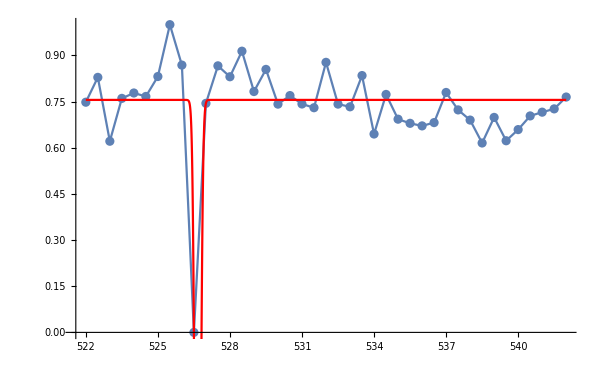
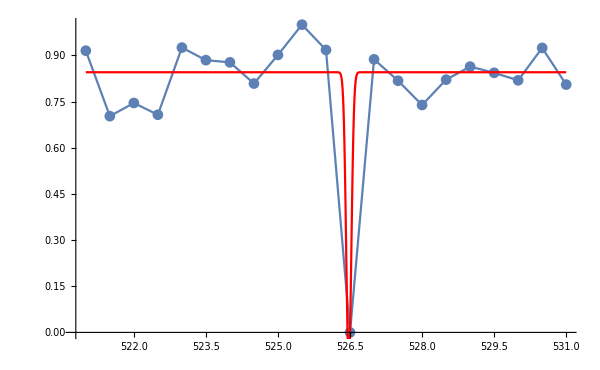
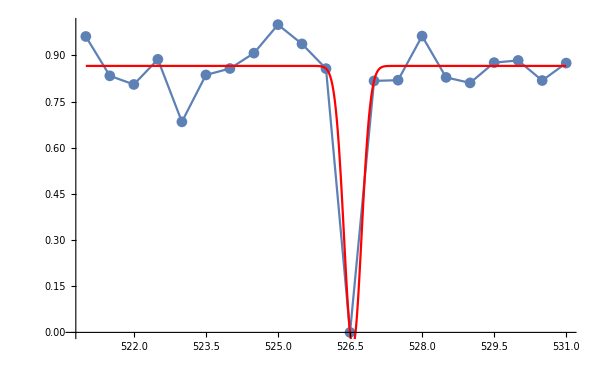
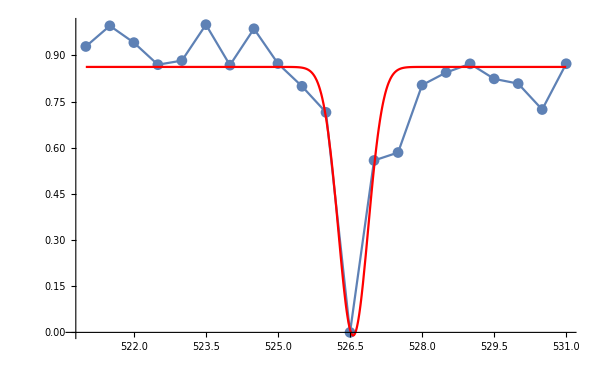
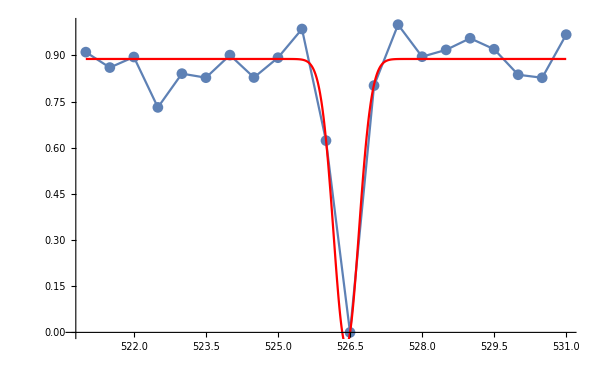
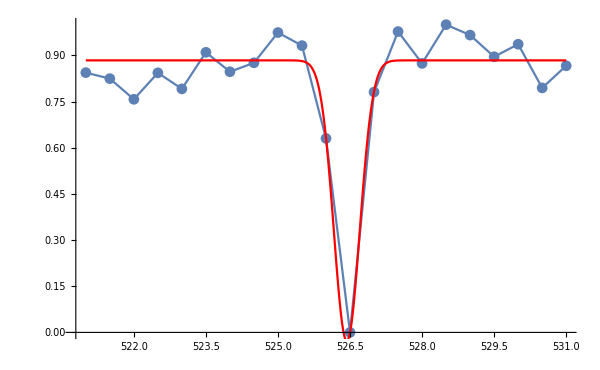
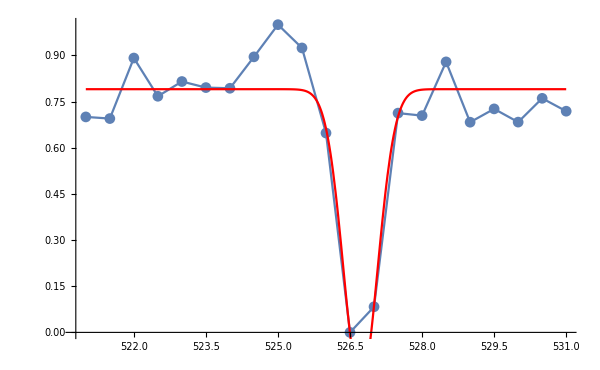
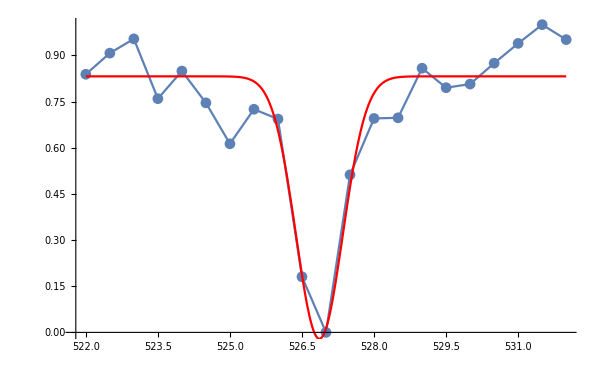

```mathematica
TableForm[FitTable202303[[All,2]]]
```

```mathematica
TableForm[FitTable202203[[All,2]]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]